Note: To run this file, first run /QTM/Hexagonal_Decomp, as it defines the real space displacement set, as well as computed the C6v eigenvectors used to decompose the measurement

### Hexagonal Grid

```mathematica
ℛUC=Polygon[1/(√3)Table[({Cos[2 Pi k/6+0π/2],Sin[2 Pi k/6+0π/2]}),{k,6}]];

h[x_,y_,0]:=Prepend[Table[{Cos[2 Pi k/6+0π/2]+x,Sin[2 Pi k/6+0π/2]+y},{k,6}],{0,0}]

hexGrid[N_Integer?NonNegative]:=Flatten[Table[{i+j/2,Sqrt[3] j/2},{i,-N,N},{j,Max[-N,-i-N],Min[N,-i+N]}],1];


ΛN=10;

UCmesh=(2 Sqrt[2]/Sqrt[3])*hexGrid[ΛN]/(ΛN+1);

kList=DeleteCases[UCmesh,{0,0}];
```

### Parameters

```mathematica
w1=1;
w0=0.75w1;
μ=0.5;
mv=-0.5;
epsx=0.1;
epsy=-0.1;

a=1.42Sqrt[3];
thetaTwist=1.05Degree;
Ktheta=(4 Pi/(3 a)) 2 Sin[thetaTwist/2];
q0=Ktheta {0.6,0.8};

gammaT=0.02 w1;
gammaS=0.02 w1;

biasEnergy=1. w1;      
dBias=0.001 w1;         

deltaTip0=1. w1;
deltaSample0=1. w1;

qList={q0};

G[1]={0,0};

G[2]=(4 Pi/(3 a)) {-3/2,Sqrt[3]/2};

G[3]=(4 Pi/(3 a)) {-3/2,-Sqrt[3]/2};
```

### Order Parameters

```mathematica
GapScale[x_?NumericQ]:=Which[x<=0,1.,x>=1,0.,True,Tanh[1.74 Sqrt[1/x-1]]];

GapTip[k_,t_?NumericQ]:=deltaTip0(* GapScale[t]*);

GapSample[k_,t_?NumericQ]:=deltaSample0 GapScale[t] (1+0(k[[1]]+0.5 k[[2]]+0I k[[2]]));
```

### Functions

```mathematica
ξT[k_,τ_]:=-μ+mv τ+Norm[k]+epsx(k[[1]]^2-k[[2]]^2)+epsy k[[1]]* k[[2]];
ξS[k_,τ_]:=-μ+Norm[k];


th[k_]:=ArcTan[k[[1]],k[[2]]];

phi[j_]:=2Pi(j-1)/3;




ElectronSpectral[xi_?NumericQ,delta_?NumericQ,omega_?NumericQ,gamma_?NumericQ]:=Module[{energy,u2,v2},energy=Sqrt[xi^2+Abs[delta]^2];
If[energy==0,Return[gamma/(Pi (omega^2+gamma^2))]];
u2=(1+xi/energy)/2;
v2=(1-xi/energy)/2;
(gamma/Pi)*(u2/((omega-energy)^2+gamma^2)+v2/((omega+energy)^2+gamma^2))];


UVPair[xi_?NumericQ,delta_?NumericQ]:=Module[{en,u,v},en=Sqrt[xi^2+Abs[delta]^2];
If[TrueQ[Abs[delta]==0],Return[If[xi>=0,{1.,0.},{0.,1.}]]];
u=Sqrt[(1+xi/en)/2];
v=Conjugate[delta]/Abs[delta] Sqrt[(1-xi/en)/2];
{u,v}];


MT[k_,q_,r_,tau_,t_?NumericQ]:=Module[{kp,thetaDelta,thetaSigma,ut,vt,us,vs},kp=k+q;
thetaDelta=(th[k]-th[kp])/2;
thetaSigma=(th[k]+th[kp])/2;
{ut,vt}=UVPair[N[ξT[kp,tau]],GapTip[kp,t]];
{us,vs}=UVPair[N[ξS[k,tau]],GapSample[k,t]];
(ut us-Conjugate[vt] vs)*Sum[(w0 Cos[thetaDelta]+w1 tau Cos[tau phi[j]+thetaSigma])*Exp[I tau G[j].r],{j,1,3}]];


AT[k_,omega_?NumericQ,tau_,t_?NumericQ]:=ElectronSpectral[ξT[k,tau],GapTip[k,t],omega,gammaT];

AS[k_,omega_?NumericQ,tau_,t_?NumericQ]:=ElectronSpectral[ξS[k,tau],GapSample[k,t],omega,gammaS];


EnergyOverlap[k_,q_,tau_,t_?NumericQ,b_?NumericQ]:=Module[{kp,enT,enS,lo,hi,cuts,integrand,omega},If[TrueQ[b==0],Return[0.]];
kp=k+q;
enT=N[Sqrt[ξT[kp,tau]^2+Abs[GapTip[kp,t]]^2]];
enS=N[Sqrt[ξS[k,tau]^2+Abs[GapSample[k,t]]^2]];
lo=N[Min[-b,0.]];
hi=N[Max[-b,0.]];
cuts=Sort[DeleteDuplicates[Join[{lo,hi},Select[N[{-enS,enS,-b-enT,-b+enT}],lo<#<hi&]]]];
integrand[omega_?NumericQ]:=AT[kp,omega+b,tau,t]*AS[k,omega,tau,t];
Sign[b]*NIntegrate[integrand[omega],Evaluate[Prepend[cuts,omega]],Method->{"GlobalAdaptive","SymbolicProcessing"->0},AccuracyGoal->8,PrecisionGoal->6,MaxRecursion->20]];


CurrentVector[t_?NumericQ,b_?NumericQ]:=Module[{weights},weights=Table[EnergyOverlap[kList[[ik]],qList[[iq]],1,t,b],{ik,Length[kList]},{iq,Length[qList]}];
Table[Sum[weights[[ik,iq]]*Abs[MT[kList[[ik]],qList[[iq]],r,1,t]]^2,{ik,Length[kList]},{iq,Length[qList]}],{r,points}]];



(*----------Symmetry decomposition----------*)

evA1=Eigenvectors[Subscript[P,A1]][[1]];
evA2=Eigenvectors[Subscript[P,A2]][[1]];
evB1=Eigenvectors[Subscript[P,B1]][[1]];
evB2=Eigenvectors[Subscript[P,B2]][[1]];

evE1=Take[Eigenvectors[Subscript[P,E1]],4];
evE2=Take[Eigenvectors[Subscript[P,E2]],4];


SymmetryWeights[vec_]:=Module[{a1,a2,b1,b2,e1,e2},
a1=evA1.vec/e20;
a2=Chop[(evA2.vec)/e20,10^-12];
b1=Chop[(evB1.vec)/e20,10^-12];
b2=Chop[(evB2.vec)/e20,10^-12];
e1=Chop[((#.vec)/e20&)/@evE1,10^-12];
e2=Chop[-((#.vec/e20)&)/@evE2,10^-12];
{a1,a2,b1,b2,e1,e2}]



tList=N[Range[0.98,1.02,0.002]];

kList=N[kList];
qList=N[qList];


If[$KernelCount==0,LaunchKernels[]];


ConductanceVector[t_?NumericQ]:=(CurrentVector[t,biasEnergy+dBias]-CurrentVector[t,biasEnergy-dBias])/(2 dBias);
e20=Norm[(#.ConductanceVector[1.01]&)/@evE2];


DistributeDefinitions[EnergyOverlap,CurrentVector,ConductanceVector,MT,AT,AS,ElectronSpectral,GapScale,GapTip,GapSample,UVPair,momentumPairs,biasEnergy,dBias];

conductanceVectors=Monitor[ParallelTable[ConductanceVector[tList[[i]]],{i,Length[tList]}],Row[{"Temperature point: ",i," / ",Length[tList]}]];

(*Symmetry decomposition*)
results=SymmetryWeights/@conductanceVectors;

A1vals=Abs[results[[All,1]]];
A2vals=Abs[results[[All,2]]];
B1vals=Abs[results[[All,3]]];
B2vals=Abs[results[[All,4]]];

E1vals=Norm/@results[[All,5]];
E2vals=Norm/@results[[All,6]];
```

### Plotting

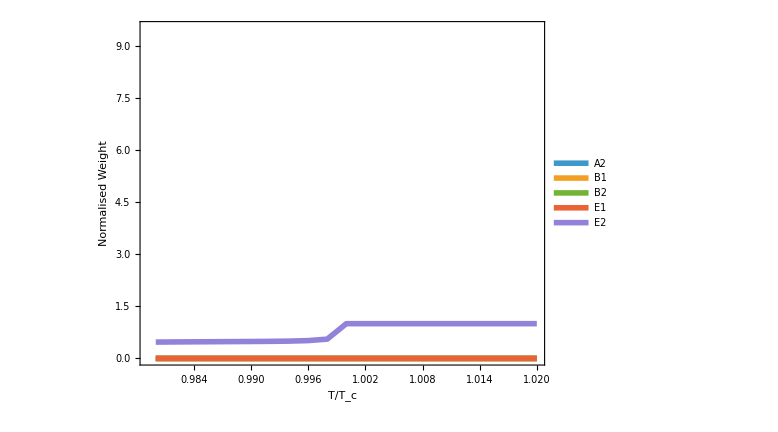

```mathematica
ListLinePlot[{Transpose[{tList,A2vals}],Transpose[{tList,B1vals}],Transpose[{tList,B2vals}],Transpose[{tList,E1vals}],Transpose[{tList,E2vals}]},
PlotRange->{0,9.5},
PlotLegends->Placed[Style[#,20,FontFamily->"Times New Roman",Black]&/@{"A2","B1","B2","E1","E2"},{0.8,0.65}],
Frame->True,
Axes->False,
FrameStyle->Directive[Black,Thick],
FrameLabel->{Style[" T/\!\(\*SubscriptBox[\(T\), \(c\)]\)",24,FontFamily->"Times New Roman",Black],Style["Normalised Weight",24,FontFamily->"Times New Roman",Black]},
LabelStyle->Directive[Black,18,FontFamily->"Times New Roman"],
PlotStyle->AbsoluteThickness[4],AspectRatio->0.75,ImageSize->Large]
```